```mathematica
(*Mathematica*)
```

```mathematica
Clear[s,w]
```

```mathematica
(*First so(5)*)
s[1]={{0,1,0,0,0},
           {1,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[2]={{0,0,1,0,0},
           {0,0,0,0,0},
          {1,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[3]={{0,0,0,1,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0},
{0,0,0,0,0}};
s[4]={{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0}};
s[5]={{0,0,0,0,0},
{0,0,1,0,0},
{0,1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[10]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,1},
        { 0,0,0,1,0}};
s[9]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,1,0,0}};
s[8]={{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,1,0,0,0}};
s[7]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,1,0},
{0,0,1,0,0},
{0,0,0,0,0}};
s[6]={{0,0,0,0,0},
{0,0,0,1,0},
{0,0,0,0,0},
{0,1,0,0,0},
{0,0,0,0,0}};
(* second so(5) *)
s[11]={{0,I,0,0,0},
           {-I,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[12]={{0,0,-I,0,0},
           {0,0,0,0,0},
          {I,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[13]={{0,0,0,I,0},
{0,0,0,0,0},
{0,0,0,0,0},
{-I,0,0,0,0},
{0,0,0,0,0}};
s[14]={{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{I,0,0,0,0}};
s[15]={{0,0,0,0,0},
{0,0,I,0,0},
{0,-I,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[20]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,I},
        { 0,0,0,-I,0}};
s[19]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,I,0,0}};
s[18]={{0,0,0,0,0},
{0,0,0,0,I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,-I,0,0,0}};
s[17]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,I,0},
{0,0,-I,0,0},
{0,0,0,0,0}};
s[16]={{0,0,0,0,0},
{0,0,0,-I,0},
{0,0,0,0,0},
{0,I,0,0,0},
{0,0,0,0,0}};
(* DIAGONAL four: n-1 matrices*)
(* zero trace with normalization Sqrt[n*(n-1)/2]*)
s[21]={{1,0,0,0,0},
{0,-1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[22]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,-2,0,0},
{0,0,0,0,0},
{0,0,0,0,-1}}/Sqrt[7/2];
s[23]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,1,0,0},
{0,0,0,-3,0},
{0,0,0,0,0}}/Sqrt[6];
s[24]={{2,0,0,0,0},
{0,2,0,0,0},
{0,0,2,0,0},
{0,0,0,-3,0},
{0,0,0,0,-3}}/√30;
s[25]=IdentityMatrix[5];
```

```mathematica
r[1]=Exp[2*Pi*I/12]
```

ⅇ^((ⅈ π)/6)

```mathematica
Table[r[i]=r[1]^i,{i,12}]
```

{ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1,ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1}

```mathematica
Table[r[i+12]=Conjugate[r[i]],{i,12}]
```

{ⅇ^(-(ⅈ π)/6),ⅇ^(-(ⅈ π)/3),-ⅈ,ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(5 ⅈ π)/6),-1,ⅇ^((5 ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅈ,ⅇ^((ⅈ π)/3),ⅇ^((ⅈ π)/6),1}

```mathematica
p[x_]=FullSimplify[ExpandAll[Product[x-r[i],{i,24}]]]
```

(-1+x^12)^2

```mathematica
r[i_]:=z/.NSolve[p[z]==0,z][[i]]
```

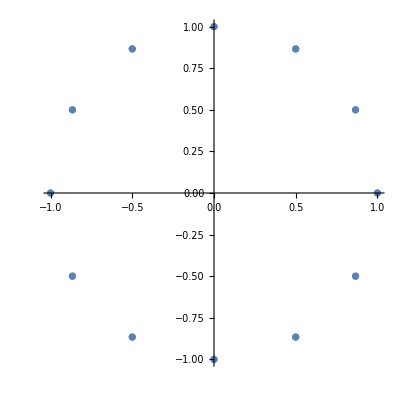

```mathematica
ComplexListPlot[Table[r[i],{i,24}]]
```

```mathematica
(*SL(5,C)Matrix normalization*)
```

```mathematica
m=(s[25]+Sum[s[i]*(r[i]),{i,24}])/(-4.016649993578978+13.299255473652707 ⅈ)^(1/5)
```

{{1.45145+0.489859 ⅈ,1.04558+0.457647 ⅈ,0.246278-0.181314 ⅈ,0.676672+0.919122 ⅈ,-0.672844+0.495358 ⅈ},{0.122626-0.280161 ⅈ,1.02106-0.610577 ⅈ,0.181314+0.246278 ⅈ,-0.919122+0.676672 ⅈ,-0.676672-0.919122 ⅈ},{0.676672+0.919122 ⅈ,-0.919122+0.676672 ⅈ,0.49625-0.651922 ⅈ,-0.495358-0.672844 ⅈ,0.246278-0.181314 ⅈ},{-0.246278+0.181314 ⅈ,-0.181314-0.246278 ⅈ,-0.672844+0.495358 ⅈ,-0.466524-0.206016 ⅈ,-0.495358-0.672844 ⅈ},{0.495358+0.672844 ⅈ,-0.246278+0.181314 ⅈ,-0.676672-0.919122 ⅈ,0.672844-0.495358 ⅈ,0.00218237-0.294516 ⅈ}}

```mathematica
N[Det[m]//Chop]
```

1.

```mathematica
Tr[m]
```

2.50442-1.27317 ⅈ

```mathematica
msl=ExpandAll[N[s[25]+Sum[s[i]*(z-r[i]),{i,24}]]/(-4.016649993578978+13.299255473652707 ⅈ)^(1/5)]
```

{{(-0.351017-0.920253 ⅈ)+(1.26986-0.496657 ⅈ) z,(-1.04558-0.457647 ⅈ)+(0.765415+0.335021 ⅈ) z,(-0.246278+0.181314 ⅈ)+(0.335021-0.765415 ⅈ) z,(-0.676672-0.919122 ⅈ)+(0.765415+0.335021 ⅈ) z,(0.672844-0.495358 ⅈ)+(0.335021-0.765415 ⅈ) z},{(-0.122626+0.280161 ⅈ)+(0.335021-0.765415 ⅈ) z,(0.0793766+0.180183 ⅈ)+(0.169423-0.0662633 ⅈ) z,(-0.181314-0.246278 ⅈ)+(0.765415+0.335021 ⅈ) z,(0.919122-0.676672 ⅈ)+(0.335021-0.765415 ⅈ) z,(0.676672+0.919122 ⅈ)+(0.765415+0.335021 ⅈ) z},{(-0.676672-0.919122 ⅈ)+(0.765415+0.335021 ⅈ) z,(0.919122-0.676672 ⅈ)+(0.335021-0.765415 ⅈ) z,(0.604186+0.221528 ⅈ)-(0.162671-0.0636226 ⅈ) z,(0.495358+0.672844 ⅈ)+(0.765415+0.335021 ⅈ) z,(-0.246278+0.181314 ⅈ)+(0.335021-0.765415 ⅈ) z},{(0.246278-0.181314 ⅈ)+(0.335021-0.765415 ⅈ) z,(0.181314+0.246278 ⅈ)+(0.765415+0.335021 ⅈ) z,(0.672844-0.495358 ⅈ)+(0.335021-0.765415 ⅈ) z,(1.56696-0.224378 ⅈ)-(0.975243-0.38143 ⅈ) z,(0.495358+0.672844 ⅈ)+(0.765415+0.335021 ⅈ) z},{(-0.495358-0.672844 ⅈ)+(0.765415+0.335021 ⅈ) z,(0.246278-0.181314 ⅈ)+(0.335021-0.765415 ⅈ) z,(0.676672+0.919122 ⅈ)+(0.765415+0.335021 ⅈ) z,(-0.672844+0.495358 ⅈ)+(0.335021-0.765415 ⅈ) z,(1.09825-0.135878 ⅈ)-(0.595471-0.232896 ⅈ) z}}

```mathematica
TableForm[msl]
```

(-0.351017-0.920253 ⅈ)+(1.26986-0.496657 ⅈ) z | (-1.04558-0.457647 ⅈ)+(0.765415+0.335021 ⅈ) z | (-0.246278+0.181314 ⅈ)+(0.335021-0.765415 ⅈ) z | (-0.676672-0.919122 ⅈ)+(0.765415+0.335021 ⅈ) z | (0.672844-0.495358 ⅈ)+(0.335021-0.765415 ⅈ) z
(-0.122626+0.280161 ⅈ)+(0.335021-0.765415 ⅈ) z | (0.0793766+0.180183 ⅈ)+(0.169423-0.0662633 ⅈ) z | (-0.181314-0.246278 ⅈ)+(0.765415+0.335021 ⅈ) z | (0.919122-0.676672 ⅈ)+(0.335021-0.765415 ⅈ) z | (0.676672+0.919122 ⅈ)+(0.765415+0.335021 ⅈ) z
(-0.676672-0.919122 ⅈ)+(0.765415+0.335021 ⅈ) z | (0.919122-0.676672 ⅈ)+(0.335021-0.765415 ⅈ) z | (0.604186+0.221528 ⅈ)-(0.162671-0.0636226 ⅈ) z | (0.495358+0.672844 ⅈ)+(0.765415+0.335021 ⅈ) z | (-0.246278+0.181314 ⅈ)+(0.335021-0.765415 ⅈ) z
(0.246278-0.181314 ⅈ)+(0.335021-0.765415 ⅈ) z | (0.181314+0.246278 ⅈ)+(0.765415+0.335021 ⅈ) z | (0.672844-0.495358 ⅈ)+(0.335021-0.765415 ⅈ) z | (1.56696-0.224378 ⅈ)-(0.975243-0.38143 ⅈ) z | (0.495358+0.672844 ⅈ)+(0.765415+0.335021 ⅈ) z
(-0.495358-0.672844 ⅈ)+(0.765415+0.335021 ⅈ) z | (0.246278-0.181314 ⅈ)+(0.335021-0.765415 ⅈ) z | (0.676672+0.919122 ⅈ)+(0.765415+0.335021 ⅈ) z | (-0.672844+0.495358 ⅈ)+(0.335021-0.765415 ⅈ) z | (1.09825-0.135878 ⅈ)-(0.595471-0.232896 ⅈ) z

```mathematica
f[z_]=ExpandAll[CharacteristicPolynomial[msl,z]/(6.321151643005932+6.866448011123357 ⅈ)]//Chop
```

(-0.24527+0.0180194 ⅈ)+(0.604835-0.22451 ⅈ) z-(3.10942-1.43592 ⅈ) z^2+(2.71256-3.14948 ⅈ) z^3-(1.94377-2.2402 ⅈ) z^4+1. z^5

```mathematica
w=z/.NSolve[f[z]==0,z]
```

{0.0121989+0.3076 ⅈ,0.101465-0.274812 ⅈ,0.234434+0.748434 ⅈ,0.372415-2.74987 ⅈ,1.22325-0.271549 ⅈ}

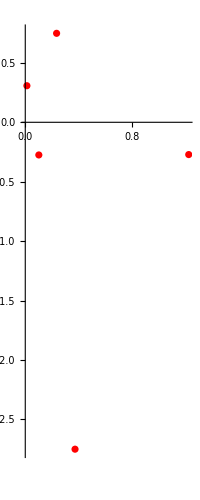

```mathematica
ComplexListPlot[w,PlotStyle->Red]
```

```mathematica
max2=Max[Norm/@w]+0.5
```

3.27497

```mathematica
ga=ComplexPlot[f[z],{z,-max2-I*max2,max2+I*max2},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
gb=ComplexPlot3D[f[z],{z,-max2-I*max2,max2+I*max2},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100,ViewPoint->Above];
```

```mathematica
g1=JuliaSetPlot[f[x]/Sqrt[3.095],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
g2=ListPlot[JuliaSetPoints[f[x]/Sqrt[3.095],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1,Background->Black];
Export["Julia_SU5_Anti_deSitter_cycle12_Polynomial_scale_Sqrt3p095_grid.jpg",GraphicsGrid[{{ga,gb}, 
 {g1,g2}},ImageSize->4000]]
```

Julia_SU5_Anti_deSitter_cycle12_Polynomial_scale_Sqrt3p095_grid.jpg

```mathematica
Clear[g1,g2]
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Sept 20026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz]/Sqrt[3.095];
        ++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-0.600001,1.6,1000},{-1.00001,1.2,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→Hue,Background→Black,ViewPoint→Above,ImageSize->{2000,2000}];
```

```mathematica
Export["j_1000_SU5_Anti_deSitter_cycle12_Polynomial_scale_Sqrt3p095_In_Out_monitor2_g1.jpg",g1]
```

j_1000_SU5_Anti_deSitter_cycle12_Polynomial_scale_Sqrt3p095_In_Out_monitor2_g1.jpg

```mathematica
g2=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> (Hue[1.75*#]&),ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU5_Anti_deSitter_cycle12_Polynomial_scale_Sqrt3p095_In_Out_monitor_g2.jpg",g2]
```

j_1000_SU5_Anti_deSitter_cycle12_Polynomial_scale_Sqrt3p095_In_Out_monitor_g2.jpg

```mathematica
colortab=Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU5_Anti_deSitter_cycle12_Polynomial_scale_Sqrt3p095__In_Out_monitor_g3.jpg",g3]
```

j_1000_SU5_Anti_deSitter_cycle12_Polynomial_scale_Sqrt3p095__In_Out_monitor_g3.jpg

```mathematica
Export["j_1000_SU5_Anti_deSitter_cycle12_Polynomial_scale_Sqrt3p095_grid2.jpg",GraphicsGrid[{{ga,g2}, 
 {g3,g1}},ImageSize->4000]]
```

j_1000_SU5_Anti_deSitter_cycle12_Polynomial_scale_Sqrt3p095_grid2.jpg

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear[s,w]
```

```mathematica
(*First so(5)*)
s[1]={{0,1,0,0,0},
           {1,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[2]={{0,0,1,0,0},
           {0,0,0,0,0},
          {1,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[3]={{0,0,0,1,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0},
{0,0,0,0,0}};
s[4]={{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0}};
s[5]={{0,0,0,0,0},
{0,0,1,0,0},
{0,1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[10]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,1},
        { 0,0,0,1,0}};
s[9]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,1,0,0}};
s[8]={{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,1,0,0,0}};
s[7]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,1,0},
{0,0,1,0,0},
{0,0,0,0,0}};
s[6]={{0,0,0,0,0},
{0,0,0,1,0},
{0,0,0,0,0},
{0,1,0,0,0},
{0,0,0,0,0}};
(* second so(5) *)
s[11]={{0,I,0,0,0},
           {-I,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[12]={{0,0,-I,0,0},
           {0,0,0,0,0},
          {I,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[13]={{0,0,0,I,0},
{0,0,0,0,0},
{0,0,0,0,0},
{-I,0,0,0,0},
{0,0,0,0,0}};
s[14]={{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{I,0,0,0,0}};
s[15]={{0,0,0,0,0},
{0,0,I,0,0},
{0,-I,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[20]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,I},
        { 0,0,0,-I,0}};
s[19]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,I,0,0}};
s[18]={{0,0,0,0,0},
{0,0,0,0,I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,-I,0,0,0}};
s[17]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,I,0},
{0,0,-I,0,0},
{0,0,0,0,0}};
s[16]={{0,0,0,0,0},
{0,0,0,-I,0},
{0,0,0,0,0},
{0,I,0,0,0},
{0,0,0,0,0}};
(* DIAGONAL four: n-1 matrices*)
(* zero trace with normalization Sqrt[n*(n-1)/2]*)
s[21]={{1,0,0,0,0},
{0,-1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[22]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,-2,0,0},
{0,0,0,0,0},
{0,0,0,0,-1}}/Sqrt[7/2];
s[23]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,1,0,0},
{0,0,0,-3,0},
{0,0,0,0,0}}/Sqrt[6];
s[24]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,1,0,0},
{0,0,0,1,0},
{0,0,0,0,-4}}/Sqrt[10];
s[25]=IdentityMatrix[5];
```

```mathematica
r[1]=Exp[2*Pi*I/12]
```

ⅇ^((ⅈ π)/6)

```mathematica
Table[r[i]=r[1]^i,{i,12}]
```

{ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1,ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1}

```mathematica
Table[r[i+12]=Conjugate[r[i]],{i,12}]
```

{ⅇ^(-(ⅈ π)/6),ⅇ^(-(ⅈ π)/3),-ⅈ,ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(5 ⅈ π)/6),-1,ⅇ^((5 ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅈ,ⅇ^((ⅈ π)/3),ⅇ^((ⅈ π)/6),1}

```mathematica
p[x_]=FullSimplify[ExpandAll[Product[x-r[i],{i,24}]]]
```

(-1+x^12)^2

```mathematica
r[i_]:=z/.NSolve[p[z]==0,z][[i]]
```

```mathematica
ComplexListPlot[Table[r[i],{i,24}]]
```

-Graphics-

```mathematica
(*SL(5,C)Matrix normalization*)
```

```mathematica
m=(s[25]+Sum[s[i]*(r[i]),{i,24}])/(21.095985115476726+52.037495518955325 ⅈ)^(1/5)
```

{{1.01626+0.520696 ⅈ,0.736663+0.4499 ⅈ,0.203094-0.110668 ⅈ,0.413019+0.757956 ⅈ,-0.554863+0.302351 ⅈ},{0.12055-0.197388 ⅈ,0.806332-0.347928 ⅈ,0.110668+0.203094 ⅈ,-0.757956+0.413019 ⅈ,-0.413019-0.757956 ⅈ},{0.413019+0.757956 ⅈ,-0.757956+0.413019 ⅈ,0.417306-0.432601 ⅈ,-0.302351-0.554863 ⅈ,0.203094-0.110668 ⅈ},{-0.203094+0.110668 ⅈ,-0.110668-0.203094 ⅈ,-0.554863+0.302351 ⅈ,0.0467199-0.292786 ⅈ,-0.302351-0.554863 ⅈ},{0.302351+0.554863 ⅈ,-0.203094+0.110668 ⅈ,-0.413019-0.757956 ⅈ,0.554863-0.302351 ⅈ,-0.279717-0.145189 ⅈ}}

```mathematica
N[Det[m]//Chop]
```

1.

```mathematica
Tr[m]
```

2.0069-0.697808 ⅈ

```mathematica
msl=ExpandAll[N[s[25]+Sum[s[i]*(z-r[i]),{i,24}]]/(21.095985115476726+52.037495518955325 ⅈ)^(1/5)]
```

{{(-0.147633-0.730621 ⅈ)+(0.981111-0.237111 ⅈ) z,(-0.736663-0.4499 ⅈ)+(0.539275+0.32935 ⅈ) z,(-0.203094+0.110668 ⅈ)+(0.32935-0.539275 ⅈ) z,(-0.413019-0.757956 ⅈ)+(0.539275+0.32935 ⅈ) z,(0.554863-0.302351 ⅈ)+(0.32935-0.539275 ⅈ) z},{(-0.12055+0.197388 ⅈ)+(0.32935-0.539275 ⅈ) z,(0.0622922+0.138003 ⅈ)+(0.112486-0.0271852 ⅈ) z,(-0.110668-0.203094 ⅈ)+(0.539275+0.32935 ⅈ) z,(0.757956-0.413019 ⅈ)+(0.32935-0.539275 ⅈ) z,(0.413019+0.757956 ⅈ)+(0.539275+0.32935 ⅈ) z},{(-0.413019-0.757956 ⅈ)+(0.539275+0.32935 ⅈ) z,(0.757956-0.413019 ⅈ)+(0.32935-0.539275 ⅈ) z,(0.451319+0.222676 ⅈ)-(0.14965-0.0361669 ⅈ) z,(0.302351+0.554863 ⅈ)+(0.539275+0.32935 ⅈ) z,(-0.203094+0.110668 ⅈ)+(0.32935-0.539275 ⅈ) z},{(0.203094-0.110668 ⅈ)+(0.32935-0.539275 ⅈ) z,(0.110668+0.203094 ⅈ)+(0.539275+0.32935 ⅈ) z,(0.554863-0.302351 ⅈ)+(0.32935-0.539275 ⅈ) z,(0.821905+0.0828605 ⅈ)-(0.39458-0.0953604 ⅈ) z,(0.302351+0.554863 ⅈ)+(0.539275+0.32935 ⅈ) z},{(-0.302351-0.554863 ⅈ)+(0.539275+0.32935 ⅈ) z,(0.203094-0.110668 ⅈ)+(0.32935-0.539275 ⅈ) z,(0.413019+0.757956 ⅈ)+(0.539275+0.32935 ⅈ) z,(-0.554863+0.302351 ⅈ)+(0.32935-0.539275 ⅈ) z,(1.14834-0.0647361 ⅈ)-(0.781516-0.188873 ⅈ) z}}

```mathematica
TableForm[msl]
```

(-0.147633-0.730621 ⅈ)+(0.981111-0.237111 ⅈ) z | (-0.736663-0.4499 ⅈ)+(0.539275+0.32935 ⅈ) z | (-0.203094+0.110668 ⅈ)+(0.32935-0.539275 ⅈ) z | (-0.413019-0.757956 ⅈ)+(0.539275+0.32935 ⅈ) z | (0.554863-0.302351 ⅈ)+(0.32935-0.539275 ⅈ) z
(-0.12055+0.197388 ⅈ)+(0.32935-0.539275 ⅈ) z | (0.0622922+0.138003 ⅈ)+(0.112486-0.0271852 ⅈ) z | (-0.110668-0.203094 ⅈ)+(0.539275+0.32935 ⅈ) z | (0.757956-0.413019 ⅈ)+(0.32935-0.539275 ⅈ) z | (0.413019+0.757956 ⅈ)+(0.539275+0.32935 ⅈ) z
(-0.413019-0.757956 ⅈ)+(0.539275+0.32935 ⅈ) z | (0.757956-0.413019 ⅈ)+(0.32935-0.539275 ⅈ) z | (0.451319+0.222676 ⅈ)-(0.14965-0.0361669 ⅈ) z | (0.302351+0.554863 ⅈ)+(0.539275+0.32935 ⅈ) z | (-0.203094+0.110668 ⅈ)+(0.32935-0.539275 ⅈ) z
(0.203094-0.110668 ⅈ)+(0.32935-0.539275 ⅈ) z | (0.110668+0.203094 ⅈ)+(0.539275+0.32935 ⅈ) z | (0.554863-0.302351 ⅈ)+(0.32935-0.539275 ⅈ) z | (0.821905+0.0828605 ⅈ)-(0.39458-0.0953604 ⅈ) z | (0.302351+0.554863 ⅈ)+(0.539275+0.32935 ⅈ) z
(-0.302351-0.554863 ⅈ)+(0.539275+0.32935 ⅈ) z | (0.203094-0.110668 ⅈ)+(0.32935-0.539275 ⅈ) z | (0.413019+0.757956 ⅈ)+(0.539275+0.32935 ⅈ) z | (-0.554863+0.302351 ⅈ)+(0.32935-0.539275 ⅈ) z | (1.14834-0.0647361 ⅈ)-(0.781516-0.188873 ⅈ) z

```mathematica
f[z_]=ExpandAll[CharacteristicPolynomial[msl,z]/(1.5671111364413322+0.6292971843425631 ⅈ)]//Chop
```

(-0.47332-0.111702 ⅈ)+(0.542665+0.709122 ⅈ) z-(3.51925+3.57406 ⅈ) z^2+(6.85387+1.50779 ⅈ) z^3-(5.00089-1.16852 ⅈ) z^4+1. z^5

```mathematica
w=z/.NSolve[f[z]==0,z]
```

{-0.0426273-0.253952 ⅈ,0.00426232+0.763039 ⅈ,0.274578+0.464711 ⅈ,1.08568-0.149801 ⅈ,3.679-1.99252 ⅈ}

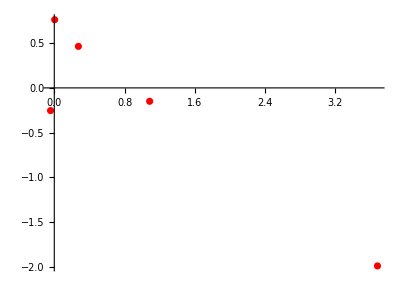

```mathematica
ComplexListPlot[w,PlotStyle->Red]
```

```mathematica
max2=Max[Norm/@w]+0.5
```

4.68392

```mathematica
ga=ComplexPlot[f[z],{z,-max2-I*max2,max2+I*max2},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
gb=ComplexPlot3D[f[z],{z,-max2-I*max2,max2+I*max2},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100,ViewPoint->Above];
```

```mathematica
g1=JuliaSetPlot[f[x]/2.75,x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
g2=ListPlot[JuliaSetPoints[f[x]/2.75,x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1,Background->White];
Export["Julia_SU5_deSitter_cycle12_Polynomial_scale_2p75_grid.jpg",GraphicsGrid[{{ga,gb}, 
 {g1,g2}},ImageSize->4000]]
```

Julia_SU5_deSitter_cycle12_Polynomial_scale_2p75_grid.jpg

```mathematica
Clear[g1,g2]
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Sept 20026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz]/2.75;
        ++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-0.600001-0.125,1.75,1000},{-0.75001-0.125,1.6,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→Hue,Background→Black,ViewPoint→Above,ImageSize->{2000,2000}];
```

```mathematica
Export["j_1000_SU5_deSitter_cycle12_Polynomial_scale_2p75_In_Out_monitor2_g1.jpg",g1]
```

j_1000_SU5_deSitter_cycle12_Polynomial_scale_2p75_In_Out_monitor2_g1.jpg

```mathematica
g2=ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction-> (Hue[1.75*#]&),ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU5_SU5_deSitter_cycle12_Polynomial_scale_2p75In_Out_monitor_g2.jpg",g2]
```

j_1000_SU5_SU5_deSitter_cycle12_Polynomial_scale_2p75In_Out_monitor_g2.jpg

```mathematica
colortab=Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->{2000,2000},Frame->False];
```

```mathematica
Export["j_1000_SU5_deSitter_cycle12_Polynomial_scale_2p75_In_Out_monitor_g3.jpg",g3]
```

j_1000_SU5_deSitter_cycle12_Polynomial_scale_2p75_In_Out_monitor_g3.jpg

```mathematica
Export["j_1000_SU5_SU5_deSitter_cycle12_Polynomial_scale_2p75_grid.jpg",GraphicsGrid[{{ga,g2}, 
 {g3,g1}},ImageSize->4000]]
```

j_1000_SU5_SU5_deSitter_cycle12_Polynomial_scale_2p75_grid.jpg

```mathematica
(*end*)
```